```mathematica
<<QMRITools`
```

### Simulating a Single 21 P spectra

#### Define the simulation parameters

```mathematica
(*metabolites and their relative amplitudes*)
met={{"PE",17},{"PC",30},{"Piex",39},{"Piin",78},{"GPE",0},{"GPC",64},{"PCr",1000},{"ATP",240},{"NAD",18},{"UDPG",20}};

nsamp=1000;(*number of spectral samples*)
bw=5000;(*acquisition bandwithd*)
field=3;(*field strenght of simulations*)
nuc="31P";(*relevant nucleius*)

snr=20;(*the target SNR*)

(*derived parameters*)
dw=1./bw;  (*dwell time*)
gyro=GetGyro[field,nuc];

metNames=met[[All,1]];
metAmps=met[[All,2]];
```

#### Getting the metabolite basis functions

```mathematica
(*get the basis functions for each *)
{names,fids,specs,table}=GetSpectraBasisFunctions[metNames,
BasisSequence->{"PulseAcquire",0}(*sequence and echo time, normally 2 dwell times*)
,SpectraSamples->nsamp,SpectraBandwith->bw,SpectraPpmShift->0,SpectraFieldStrength->field,SpectraNucleus->nuc];
(*get the timing of the sequence*)
time=GetTimeRange[fids[[1]],dw];
```

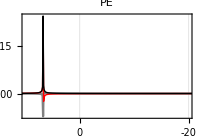
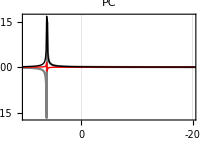
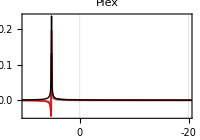
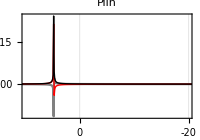
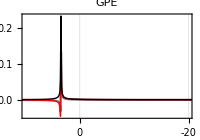
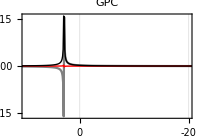
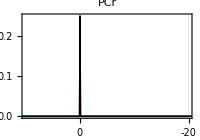
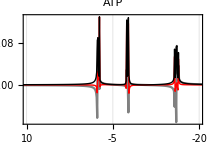

```mathematica
(*the perfect spectra and fids for each metabolite*)
PlotSpectra[#[[1]],{dw,gyro},Method -> "Re", PlotRange->{{10,-20},Full},ImageSize->200,AspectRatio->0.7,PlotLabel->#[[2]]]&/@Thread[{specs,metNames}]
PlotFid[#[[1]],dw,ImageSize->200,PlotLabel->#[[2]]]&/@Thread[{fids,metNames}]
```

#### Adding linewidth and ppm shift

```mathematica
(*add linewidth to spectra*)
fidsT=TimeShiftFid[#,time,50]&/@fids;
specsT=ShiftedFourier/@fidsT;
```

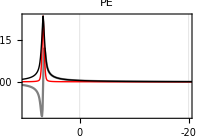
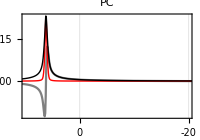
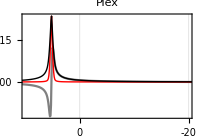
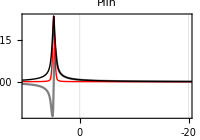
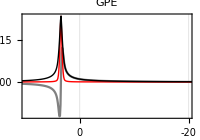
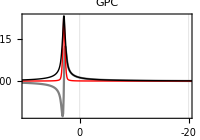
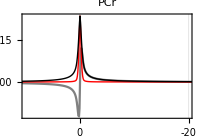
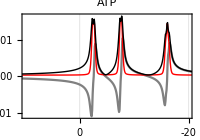

```mathematica
(*the apodized spectra and fids for each metabolite*)
PlotSpectra[#[[1]],{dw,gyro},PlotRange->{{10,-20},Full},ImageSize->200,AspectRatio->0.7,PlotLabel->#[[2]]]&/@Thread[{specsT,metNames}]
PlotFid[#[[1]],dw,ImageSize->200,PlotLabel->#[[2]]]&/@Thread[{fidsT,metNames}]
```

```mathematica
(*Shift spectra with random ppm*)
specsTS=ShiftSpectra[#,{dw,gyro},RandomReal[{-1,1}]]&/@specsT;
fidsTS=ShiftedInverseFourier/@specsTS;
```

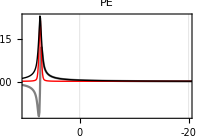
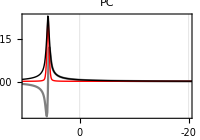
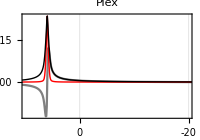
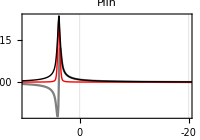
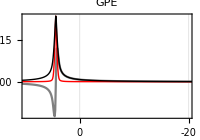
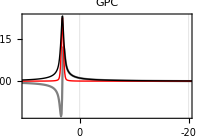
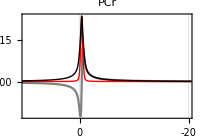
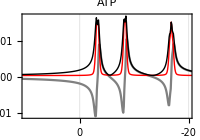

```mathematica
(*the apodized and shifted spectra and fids for each metabolite*)
PlotSpectra[#[[1]],{dw,gyro},PlotRange->{{10,-20},Full},ImageSize->200,AspectRatio->0.7,PlotLabel->#[[2]]]&/@Thread[{specsTS,metNames}]
PlotFid[#[[1]],dw,ImageSize->200,PlotLabel->#[[2]]]&/@Thread[{fidsTS,metNames}]
```

#### Adding the individual metabolites together

```mathematica
(*add all spectra together with correc amplitude*)
spec=metAmps.specsTS;
fid=ShiftedInverseFourier[spec];
```

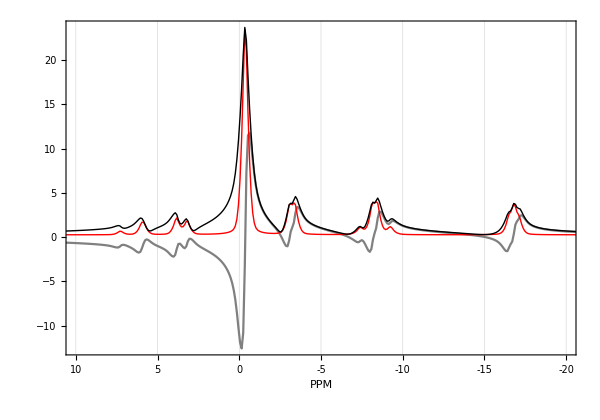
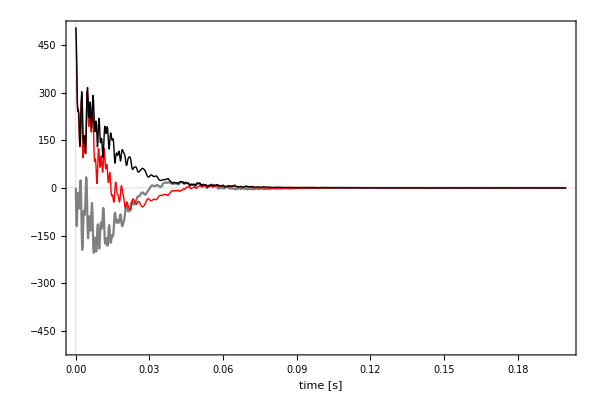

```mathematica
(*The total fid and spectra*)
{PlotSpectra[spec,{dw,gyro},PlotRange->{{10,-20},Full},ImageSize->600,AspectRatio->0.7],PlotFid[fid,dw,ImageSize->600,AspectRatio->0.7]}
```

#### Adding Noise

```mathematica
(*lets define the SNR relative to the max signal*)
sigma=Abs[First[fid]]/snr;

(*Add Noise to the Fid*)
fidN=AddNoise[fid,sigma,NoiseType->"Complex"];
specN=ShiftedFourier[fidN];
```

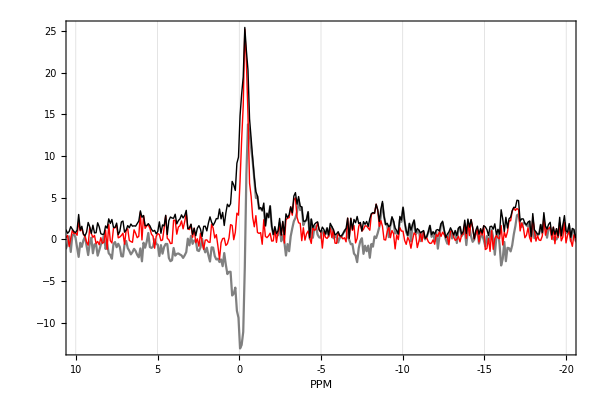
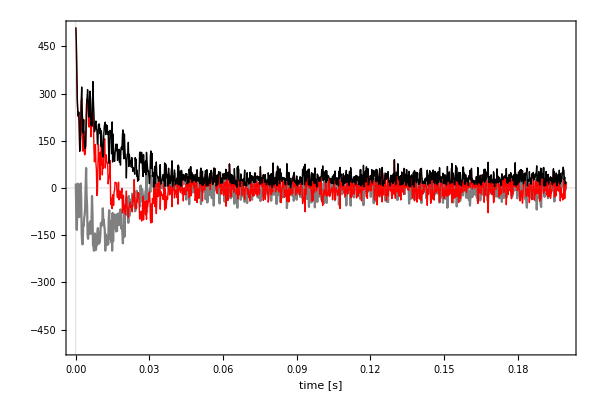

{{Null},{□}}

```mathematica
(*The total fid and spectra with noise*)
{PlotSpectra[specN,{dw,gyro},PlotRange->{{10,-20},Full},ImageSize->600,AspectRatio->0.7],PlotFid[fidN,dw,ImageSize->600,AspectRatio->0.7]}
```

```mathematica
$UserBaseDirectory
```

/home/jeroen/.Mathematica

```mathematica
SystemOpen@$UserBaseDirectory
```